## Renger Spektraldichte

```mathematica
J[w_,s1_,s2_,w1_,w2_]:=If[w<0,0,s1/(7! 2 w1^4)w^3 Exp[-√(w/w1)]+s2/(7! 2 w2^4)w^3 Exp[-√(w/w2)]]
s1=0.8;
s2=0.5;
hq=6.582 10^-16;
hq1=1.05457 10^-34;
kb=1.3806 10^-23;
kb1=8.617 10^-5;
w1=0.069 10^-3/hq;
w2=0.24 10^-3/hq;
```

Reorganisationsenergie

```mathematica
Integrate[ hq *8065.5w J[w,s1,s2,w1,w2],{w,0,∞}]
```

101.741

Normierung

```mathematica
Integrate[1/(s1+s2)J[w,s1,s2,w1,w2],{w,0,∞}]
```

1.

```mathematica
hq *8065.5*(2Pi 3 10^10)
```

1.00067

## Drude Spektraldichte

```mathematica
JDrude[ω_,γ_]:=2/(π ω)γ/(γ^2+ω^2)
```

```mathematica
Integrate[ω JDrude[ω,100],{ω,0,∞}]
```

1

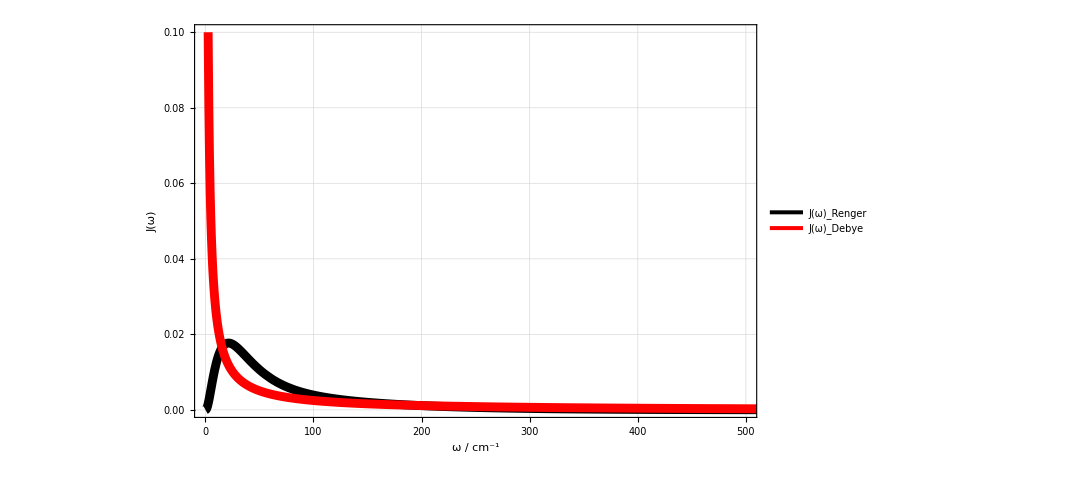

```mathematica
SpecDensPlot=Plot[ {J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)],240JDrude[w,600]},{w,0.1,2000},

FrameLabel->Map[Style[#,Black]&,{{"J(ω)",""},{"ω / cm^-1",""}},{2}],
PlotRange->{{0,500},{0,0.1}},
PlotStyle->{{Black,Thickness[0.008]},{Red,Thickness[0.008]},{Blue,Thickness[0.008]},{Purple,Thickness[0.008]}},
LabelStyle->30,Frame->True,FrameStyle->Thickness[0.0035],
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},
GridLines->{Automatic,Automatic},
GridLinesStyle->Directive[GrayLevel[0.4,0.5],AbsoluteThickness[1],AbsoluteDashing[{1,2}]],
PlotTheme->{"Detailed","Classic"},
ImageSize->800,
PlotLegends->{"J(ω)_Renger","J(ω)_Debye","ω^2/λ J(ω)_Debye"} ]
```

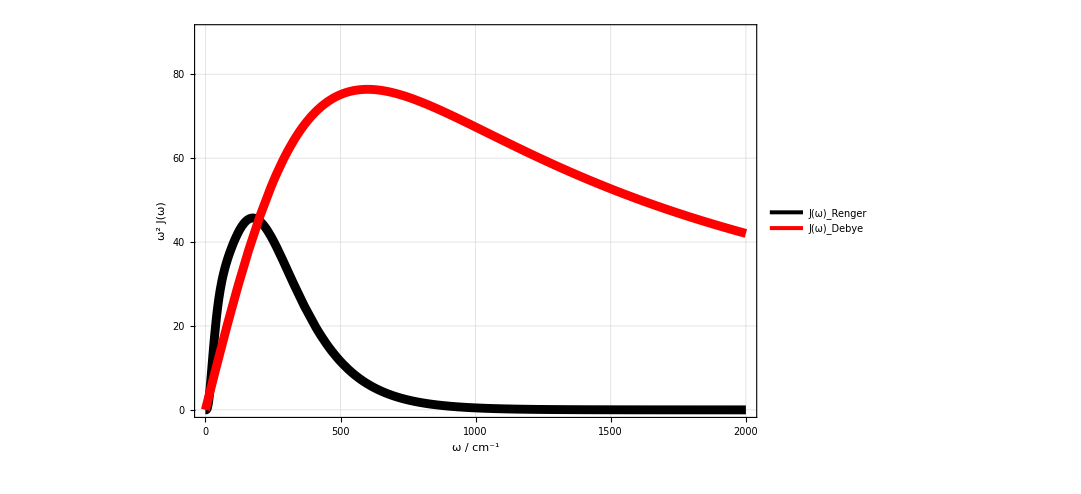

```mathematica
SpecDensRates=Plot[ {w^2 J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)],w^2 240JDrude[w,600]},{w,0,2000},

FrameLabel->Map[Style[#,Black]&,{{"ω^2 J(ω)",""},{"ω / cm^-1",""}},{2}],
PlotRange->{{0,2000},{0,90}},
PlotStyle->{{Black,Thickness[0.008]},{Red,Thickness[0.008]},{Blue,Thickness[0.008]},{Purple,Thickness[0.008]}},
LabelStyle->30,Frame->True,FrameStyle->Thickness[0.0035],
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},
GridLines->{Automatic,Automatic},
GridLinesStyle->Directive[GrayLevel[0.4,0.5],AbsoluteThickness[1],AbsoluteDashing[{1,2}]],
PlotTheme->{"Detailed","Classic"},
ImageSize->800,
PlotLegends->{"J(ω)_Renger","J(ω)_Debye","ω^2/λ J(ω)_Debye"} ]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["SpecDens.pdf",SpecDensPlot]
Export["SpecDensRate.pdf",SpecDensRates]
```

/home/lindorfer/Post-Doc/TRCD/Spectra

SpecDens.pdf

SpecDensRate.pdf

```mathematica
Manipulate[Plot[ {w^2 J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)],w^2 100(p1 JDrude[w,α]+p2 JDrude[w,β])/(p1+p2)},{w,0,2000},

FrameLabel->Map[Style[#,Black]&,{{"J(ω)",""},{"ω / cm^-1",""}},{2}],
PlotRange->{{0,2000},{0,50}},
PlotStyle->{{Black,Thickness[0.008]},{Red,Thickness[0.008]},{Blue,Thickness[0.008]},{Purple,Thickness[0.008]}},
LabelStyle->30,Frame->True,FrameStyle->Thickness[0.0035],
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks,StripTickLabels[LinTicks]}},
GridLines->{Automatic,Automatic},
GridLinesStyle->Directive[GrayLevel[0.4,0.5],AbsoluteThickness[1],AbsoluteDashing[{1,2}]],
PlotTheme->{"Detailed","Classic"},
ImageSize->800,
PlotLegends->{"J(ω)_Renger","J(ω)_Debye","ω^2/λ J(ω)_Debye"} ],{p1,0.1,2,0.1},{p2,0.1,2,0.1},{α,40,200,10},{β,40,200,10}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lindorfer/Doktorarbeit/PumpTest/Pump-Test-CD

```mathematica
Export["SpectralDensities.pdf",SpectralDensities]
```

SpectralDensities.pdf

```mathematica
Integrate[w^2JDrude[w,γ] ,w]
```

(γ Log[w^2+γ^2])/π

```mathematica
Integrate[w 100JDrude[w,53],{w,0,∞}]
```

100

```mathematica
FindMinimum[w^2( J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)]-100JDrude[w,100]),w]
```

{-5.67499,{w→14.8813}}

```mathematica
tab=Table[{w,Abs[w^2( J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)]-100JDrude[w,100])]},{w,0.1,2000}];
```

```mathematica
f=Interpolation[tab]
```

InterpolatingFunction[{{0.1, 1999.1}}, <>]

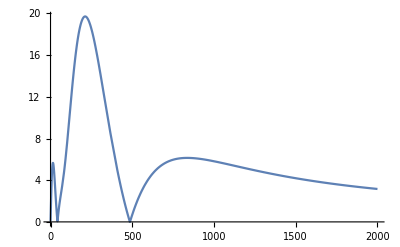

```mathematica
Plot[f[x],{x,0.1,2000},PlotRange->All]
```

```mathematica
Integrate[f[x],{x,0.1,1500}]
```

9934.5

```mathematica
Module[{tab,f},
tab=Table[{w,Abs[w^2( J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)]-100JDrude[w,100])]},{w,0.1,2000}]//N;
f=Interpolation[tab];
NIntegrate[f[x],{x,0.1,1500}]
]
```

9934.5

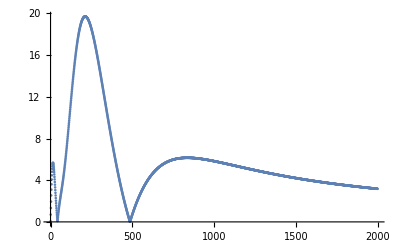

```mathematica
ListPlot[tab,PlotRange->All]
```

```mathematica
NIntegrate[Abs[w^2( J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)]-100(p1 JDrude[w,α]+ p2 JDrude[w,β])/(p1+p2))],{w,0.1,1500}]/.{α->100,β->100,p1->1,p2->1}
```

NIntegrate::inumr: The integrand Abs[w^2 (-(100 ((2 p1 α)/(π w Plus[«2»])+(2 p2 β)/(π w Plus[«2»])))/(p1+p2)+If[w<0,0,(0.8 Power[«2»]) w^3 Exp[Times[«2»]]+(0.5 Power[«2»]) w^3 Exp[Times[«2»]]])] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.1,1500}}.

9934.48

```mathematica
ParallelTable[{α,β,NIntegrate[Abs[w^2( J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)]-100(p1 JDrude[w,α]+ p2 JDrude[w,β])/(p1+p2))],{w,0.1,1500}]},{α,40,200,10},{β,40,200,10},{p1,0.1,1,0.1},{p2,0.1,1,0.1}]//Quiet
```

$Aborted

```mathematica
ParallelTable[{α,NIntegrate[Abs[w^2( J[w,s1,s2,w1/(2 Pi 3 10^10),w2/(2 Pi 3 10^10)]-100(JDrude[w,α]+JDrude[w,β])/2)],{w,0.1,1500}]},{α,40,200,10},{β,40,200,10},{p1,0.1,1,0.1},{p2,0.1,1,0.1}]//Quiet
```

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    11332.4 and 0.0144239 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    11033.9 and 0.0257658 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    11258.3 and 0.0225726 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    10520.3 and 0.0167735 for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    11186.9 and 0.0183962 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {67.1154}. NIntegrate obtained 
    10675.9 and 0.138271 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {59.4909}. NIntegrate obtained 
    11471.6 and 0.011728 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {67.056}. NIntegrate obtained 
    10615.1 and 0.579751 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {63.3608}. NIntegrate obtained 
    10557. and 0.0436677 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    11332.4 and 0.0144239 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {67.056}. NIntegrate obtained 
    10355.2 and 0.625008 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {63.3761}. NIntegrate obtained 
    10711.9 and 0.0121324 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {63.3608}. NIntegrate obtained 
    10305.7 and 0.0279657 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    11204.5 and 0.022843 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    10179.5 and 0.0183809 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {65.2809}. NIntegrate obtained 
    10601.4 and 0.0166977 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    10137.9 and 0.0123227 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {61.4459}. NIntegrate obtained 
    10099.1 and 0.0108902 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {55.5083}. NIntegrate obtained 
    10505.1 and 0.0260709 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {51.4183}. NIntegrate obtained 
    10576.3 and 0.0524844 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {51.4183}. NIntegrate obtained 
    10675.8 and 0.0699678 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {51.4183}. NIntegrate obtained 
    10781. and 0.0165915 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    10906.9 and 0.0512881 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {67.056}. NIntegrate obtained 
    10461.6 and 0.269097 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {51.4183}. NIntegrate obtained 
    10624.5 and 0.0369283 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {51.4183}. NIntegrate obtained 
    10731.5 and 0.0326043 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {55.4923}. NIntegrate obtained 
    10408.7 and 0.0251308 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {51.4183}. NIntegrate obtained 
    10576.3 and 0.0698472 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {51.3856}. NIntegrate obtained 
    10685.2 and 0.0720784 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    10814. and 0.0296792 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    10772.8 and 0.0217491 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {55.5083}. NIntegrate obtained 
    10311.5 and 0.0157224 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {53.4824}. NIntegrate obtained 
    10299.6 and 0.0143086 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {53.4824}. NIntegrate obtained 
    10263.8 and 0.0159011 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {59.4439}. NIntegrate obtained 
    9863.95 and 0.0226693 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {51.4183}. NIntegrate obtained 
    9858.46 and 0.0134923 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    11049.2 and 0.0766277 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    11207.7 and 0.0409041 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    11379.9 and 0.0334037 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    11003.3 and 0.0183364 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    11163.5 and 0.0823911 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    10960.6 and 0.0470293 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    11122.8 and 0.0697125 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {483.375}. NIntegrate obtained 
    11298.2 and 0.0125715 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {47.2624}. NIntegrate obtained 
    11262.5 and 0.0147896 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {43.0542}. NIntegrate obtained 
    11758.4 and 0.022674 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {43.0542}. NIntegrate obtained 
    11719. and 0.0218621 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {43.0542}. NIntegrate obtained 
    11923.6 and 0.026958 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {43.0542}. NIntegrate obtained 
    11683. and 0.0270442 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {43.0542}. NIntegrate obtained 
    11889.1 and 0.0200487 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {43.0373}. NIntegrate obtained 
    11858.3 and 0.110659 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {43.0542}. NIntegrate obtained 
    11349.1 and 0.0194 for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {43.0373}. NIntegrate obtained 
    11307.3 and 0.0223175 for the integral and error estimates.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
     recursive bisections in w near {w} = {34.4715}. NIntegrate obtained 
    11366.6 and 0.0230396 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

{{{40,11701.6},{40,11622.1},{40,11545.5},{40,11471.6},{40,11400.6},{40,11332.4},{40,11267.},{40,11204.5},{40,11144.8},{40,11088.},{40,11033.9},{40,10982.6},{40,10934.2},{40,10888.4},{40,10845.4},{40,10805.2},50,{40,11425.1},{40,11470.6},{40,11517.},{40,11564.},{40,11611.7},{40,11660.},{40,11708.9},{40,11758.4},{40,11808.4},{40,11858.9},{40,11910.},{40,11961.5},{40,12013.4},{40,12065.9},{40,12118.7}},79,{1}}
 |  |  |  |